## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Equation and and Eigenvalue function

```mathematica
<<"Definitions/Teukolsky.wl"
<<"Definitions/Eigenvalues.wl"
```

```mathematica
Eq=EqRadial/.RuleKRadial;
```

```mathematica
Clear@ℰ;
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative]:=ℰ[𝓈,ℓ,-𝓂,-𝒸];
ℰ[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[-𝓈,ℓ,𝓂,𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[𝓈,ℓ,𝓂][𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer]/;(ℓ≥Max[Abs[𝓈],Abs[𝓂]]):=ℰ[𝓈,ℓ,𝓂]=Interpolation[Import@GetSWSHEigenFile[𝓈,ℓ,𝓂]]
```

## Parameter rules and equation simplification

```mathematica
RuleR={R->Function[x,rp^-s x^(-s-I χ/τ)f[x]]};
EquationF=PowerExpand@Simplify[x^(s+I χ/τ)x (x+τ) (Eq/.RuleR)];

(* 3 different ways of obtaining the Eigenvalues of Teukolsky equation (most defined in SWSH.wl, faster is ℰ interpolation) *)
RuleBoundaryBH={𝒶[0]->1,𝒷[0]->(-ℬ τ^2)/(4 (ⅈ τ/2+χ) χ)};
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+s(s+1))^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+EigenE-s(s+1)};

(* 3 different ways of obtaining the Eigenvalues of Teukolsky equation (most defined in SWSH.wl, faster is ℰ interpolation) *)
RuleEigenParamCoef={EigenE->(EigenCoef/.Ruleκpm).Table[((𝒥 ω̄)/rp)^(n-1),{n,Length@EigenCoef}]+s(s+1)};
RuleEigenParamLeaver={EigenE->EigenLeaver[s,l,m,(𝒥 ω̄)/rp]};
RuleEigenParam={EigenE->ℰ[s,l,m,(𝒥 ω̄)/rp]};

(* Faster way to change between Eigenvalue rules *)
RuleAllParams=RuleParams~Join~RuleEigenParam;
```

```mathematica
(* Function to replace all parameters accordingly *)
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_]:=PowerExpand[(#1/.RuleBoundaryBH)//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}]&;
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_,𝓌_]:=PowerExpand[(#1/.RuleBoundaryBH)//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}]&;
```

```mathematica
(* Coeficients to estimate f and f' close to BH horizon *)
nCoef=8;
RuleF={f->Function[x,∑_(n=0)^nCoef 𝒶[n] x^n]};
FSeriesCoef=First@Solve[CoefficientList[EquationF/.RuleF,x][[2;;nCoef+1]]==0,Table[𝒶[n],{n,1,nCoef}]//Evaluate];
```

```mathematica
(EigenCoef/.Ruleκpm).Table[((𝒥 ω̄)/rp)^(n-1),{n,Length@EigenCoef}]
```

l+l^2-s (1+s)-(2 m s^2 𝒥 ω̄)/(l (1+l) rp)+(𝒥^2 (-1-((l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 l^3 (-1/4+l^2))+(((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (1+l)^3 (-1/4+(1+l)^2))) (ω̄)^2)/rp^2+(𝒥^3 ((m s^2 (l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/((-1+l) l^5 (1+l) (-1/4+l^2))-(m s^2 ((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(l (1+l)^5 (2+l) (-1/4+(1+l)^2))) (ω̄)^3)/rp^3+1/rp^4 𝒥^4 (m^2 s^4 (-(2 (l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/((-1+l)^2 l^7 (1+l)^2 (-1/4+l^2))+(2 ((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(l^2 (1+l)^7 (2+l)^2 (-1/4+(1+l)^2)))+(((-1+l)^2-s^2) (l^2-s^2) ((-1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(8 (-1/4+(-1+l)^2) (-1+l)^2 l^4 (-1+2 l) (-1/4+l^2))-((l^2-s^2)^2 (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2 (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2)/(8 l^7 (-1/4+l^2)^2)+((l^2-s^2) ((1+l)^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(8 l^4 (1+l)^4 (-1/4+l^2) (-1/4+(1+l)^2))+(((1+l)^2-s^2)^2 ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2 ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2)/(8 (1+l)^7 (-1/4+(1+l)^2)^2)-(((1+l)^2-s^2) ((2+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(8 (1+l)^4 (2+l)^2 (3+2 l) (-1/4+(1+l)^2) (-1/4+(2+l)^2))) (ω̄)^4+1/rp^5 𝒥^5 (m^3 s^6 ((4 (l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/((-1+l)^3 l^9 (1+l)^3 (-1/4+l^2))-(4 ((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(l^3 (1+l)^9 (2+l)^3 (-1/4+(1+l)^2)))+m s^2 ((3 (l^2-s^2)^2 (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2 (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2)/(4 (-1+l) l^9 (1+l) (-1/4+l^2)^2)-(3 ((1+l)^2-s^2)^2 ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2 ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2)/(4 l (1+l)^9 (2+l) (-1/4+(1+l)^2)^2)+((7+3 l) ((1+l)^2-s^2) ((2+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(4 l (1+l)^6 (2+l)^3 (3+l) (3+2 l) (-1/4+(1+l)^2) (-1/4+(2+l)^2)))+1/(2 l^3 (-1/4+l^2))m s^2 (l^2-s^2) (-((-4+3 l) ((-1+l)^2-s^2) ((-1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (-1/4+(-1+l)^2) (-2+l) (-1+l)^3 l^3 (1+l) (-1+2 l))-((4+7 l+7 l^2) ((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (-1+l) l^3 (1+l)^6 (2+l) (-1/4+(1+l)^2))) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)) (ω̄)^5+1/rp^6 𝒥^6 ((16 m^4 s^8 (-((l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (-1+l)^4 l^7 (-1/4+l^2))+(((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (1+l)^7 (2+l)^4 (-1/4+(1+l)^2))))/(l^4 (1+l)^4)+1/(l^2 (1+l)^2)4 m^2 s^4 (((6-8 l+3 l^2) ((-1+l)^2-s^2) (l^2-s^2) ((-1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(4 (-1/4+(-1+l)^2) (-2+l)^2 (-1+l)^4 l^6 (-1+2 l) (-1/4+l^2))-(3 (l^2-s^2)^2 (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2 (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2)/(4 (-1+l)^2 l^9 (-1/4+l^2)^2)+((6+20 l+31 l^2+22 l^3+11 l^4) (l^2-s^2) ((1+l)^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(4 l^3 (1+l)^6 (2+l) (3+l)^2 (3+2 l) (-1/4+l^2) (-1/4+(1+l)^2))+(3 ((1+l)^2-s^2)^2 ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2 ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^2)/(4 (1+l)^9 (2+l)^2 (-1/4+(1+l)^2)^2)-((17+14 l+3 l^2) ((1+l)^2-s^2) ((2+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(4 (1+l)^6 (2+l)^4 (3+l)^2 (3+2 l) (-1/4+(1+l)^2) (-1/4+(2+l)^2)))+(((-1+l)^2-s^2) (l^2-s^2) (-(l ((-2+l)^2-s^2) ((-2+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-2+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(6 (-1/4+(-2+l)^2) (-2+l)^2)-(((-1+l)^2-s^2) ((-1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (-1/4+(-1+l)^2) (-1+l))+((-1+l) (-3+7 l) (l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 l^3 (-1/4+l^2))) ((-1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(16 (-1/4+(-1+l)^2) (-1+l)^3 l^5 (-1+2 l)^2 (-1/4+l^2))-((l^2-s^2)^3 (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^3 (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^3)/(16 l^11 (-1/4+l^2)^3)+1/(16 l^5 (1+l)^5 (-1/4+l^2) (-1/4+(1+l)^2))(l^2-s^2) ((1+l)^2-s^2) (-((-1+l^2) (-2+4 l+3 l^2) ((-1+l)^2-s^2) ((-1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((-1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (-1/4+(-1+l)^2) (-1+l)^3 (-1+2 l)^2)+((3+4 l+2 l^2) (l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 l^3 (-1/4+l^2))-((1+2 l^2) ((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (1+l)^3 (-1/4+(1+l)^2))) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)+(((1+l)^2-s^2)^3 ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^3 ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2)^3)/(16 (1+l)^11 (-1/4+(1+l)^2)^3)+(((1+l)^2-s^2) ((2+l)^2-s^2) (1/(1+l)(2+l) (((-3+2 l+3 l^2) (l^2-s^2) (l^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) (l^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 l^4 (-1/4+l^2))-((10+7 l) ((1+l)^2-s^2) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (1+l)^3 (-1/4+(1+l)^2))+(((2+l)^2-s^2) ((2+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(2 (2+l)^2 (-1/4+(2+l)^2)))+(((3+l)^2-s^2) ((3+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((3+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(6 (3+l)^2 (-1/4+(3+l)^2))) ((1+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(-1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((1+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2) ((2+l)^2-(1/2 Abs[-m+s]+1/2 Abs[m+s])^2))/(16 (1+l)^4 (2+l)^3 (3+2 l)^2 (-1/4+(1+l)^2) (-1/4+(2+l)^2))) (ω̄)^6

## Equation solver definition

```mathematica
(* OptionsPattern to use with SolveωF to get more precision/accuracy out of NDSolve *)
IncreasePrecision={PrecisionGoal->12,AccuracyGoal->15,MaxSteps->Automatic};
```

```mathematica
(* Definition of the solver for s=1 and s=-1 equations using boundary conditions at BH horizon *)
Clear[SolveωF];
SolveωF[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,{omega__?NumberQ},opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Block[{eqF,delω,incs,fINF,k=0,last,olist,localk},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-14.;
xINF:=2 π/Abs[ω̄]*750;

(* stuff to monitor asynchronously SolveωF using ParallelTable *)
SetSharedVariable[k];
ParallelEvaluate[last=AbsoluteTime[];localk=1];

(* using ReplaceParams once to save computation time *)
{eqF,delω,incs,fINF}=ReplaceParams[𝒿,𝓈,ℓ,𝓂][{EquationF,m Ω̄,({f[x0],f'[x0]}/.RuleF/.FSeriesCoef)/.If[𝓈<0,{𝒶->𝒷},{}],f[xINF] ⅇ^(ⅈ(𝓈 ω̄ xINF-χ/τ Log[xINF]))}];
olist=DeleteCases[{omega},{delω,0.,0}];

(* use Monitor ProgressIndicator with asynchronous refresh of calculation state *)
Monitor[ParallelTable[
(* calculation state update with suppressed output *)
localk++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];k+=localk;localk=0];
(* solving the equation using NDSolve and substituing the result *)
{𝒿,ω̄,fINF}/.First@NDSolve[{eqF==0,{f[x0],f'[x0]}==incs},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]],{ω̄,olist}],
ProgressIndicator[k,{0,Length@olist}]]
];
```

## Export data

```mathematica
Clear[FormatZ,Formatϕ]
FormatZ[ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2 Abs[𝒶[0]]^2)/(χ Abs[#3]^2),-1/(1+(χ Abs[#4]^2)/(τ^2 ω̄ Abs[𝒶[0]]^2)),Abs[#4/#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
Formatϕ[ℓ_,𝓂_]:={#1,#2,Re@#3,Im@#3,Re@#4,Im@#4}&;
```

```mathematica
Spin=Range[0.01,0.99,0.01]∪{0.995,0.999,0.9995,0.9999};
```

```mathematica
Omega=Function[𝒿,0.0001+Range@@{0,Round[(1+√(1-𝒿^2)) 0.6,0.05],Round[1/450 Round[(1+√(1-𝒿^2)) 0.6,0.05],0.0005]}];
OmegaDetailed=Function[𝒿,0.0001+Range@@{0,First@TakeSmallest[{𝒿,Round[(1+√(1-𝒿^2)) 0.6,0.05]},1],First@TakeSmallest[{Ceiling[0.01𝒿,0.0001],Round[1/450 Round[(1+√(1-𝒿^2)) 0.6,0.05],0.0005]},1]}];
```

```mathematica
Clear[PutAppendCSV,ExportAllCSV];
PutAppendCSV[file_,data_?ArrayQ]:=WriteString[file,ExportString[data,"CSV"],"\n"];
ExportAllCSV[𝒿:{__?NumberQ}|𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,OmegaF_Function,eof_String:"",opts:OptionsPattern[]]/;(And@@Thread[0<𝒿<1]&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]):=Block[{dataP,dataM,tmpPrint,spins= Flatten[{𝒿}],Ns,time,timeList,fileZ,fileϕ},
Ns=Length@spins;
fileZ=GetZFile[Abs@𝓈,ℓ,𝓂,eof];
fileϕ=GetϕFile[Abs@𝓈,ℓ,𝓂,eof];
Quiet@*DeleteFile/@{fileZ,fileϕ};
time=First@AbsoluteTiming@Do[
tmpPrint=PrintTemporary@StringRiffle[{"𝓈 = +",Abs[𝓈]", 𝒥 = ",spins⟦i⟧,"  (",2i-1," of ",2Ns,")"},""];
dataP=SolveωF[spins⟦i⟧,Abs@𝓈,ℓ,𝓂,OmegaF@spins⟦i⟧,opts]; 
NotebookDelete[tmpPrint];
tmpPrint=PrintTemporary@StringRiffle[{"𝓈 = ",-Abs[𝓈],", 𝒥 = ",spins⟦i⟧,"  (",2 i," of ",2 Ns,")"},""];
dataM=SolveωF[spins⟦i⟧,-Abs@𝓈,ℓ,𝓂,OmegaF@spins⟦i⟧,opts];
PutAppendCSV[fileZ,FormatZ[ℓ,𝓂]@@@Flatten[{dataP,dataM},{{2},{1,3}}]⟦All,{1,2,3,6}⟧];
PutAppendCSV[fileϕ,Formatϕ[ℓ,𝓂]@@@Flatten[{dataP,dataM},{{2},{1,3}}]⟦All,{1,2,3,6}⟧];
NotebookDelete[tmpPrint];
,{i,Ns}];
Quiet@*Close/@{fileZ,fileϕ};
timeList=First@QuantityMagnitude@UnitConvert[Quantity[Round@time,"Seconds"],MixedUnit[{"Hours","Minutes","Seconds"}]];
Print[StringRiffle[{"Completed",eof,"files with (𝓈,ℓ,m)="}]<>StringRiffle[{Abs@𝓈,ℓ,𝓂},{"(",",",")"}]<>StringRiffle[{" for",Ns,"spin(s)"}]<>StringJoin@@Riffle[{" in ","h ","m ","s"},ToString/@MapAt[IntegerString[#,10,2]&,timeList,{{2},{3}}]]];
]
```

```mathematica
(*ExportAllCSV[0.99,1,1,1,Omega,"test2"]*)
```

```mathematica
(*ExportAllCSV[1,1,1,{0.995,0.999,0.9995,0.9999},Omega,"precision",IncreasePrecision]*)
```

## Calculate angular In/Out flux

```mathematica
Mollweide:=Graphics[#/.{ϕ_Real,θ_Real}:>{2/Pi(ϕ-Pi)Sin[θ],Cos[θ]}]&
```

```mathematica
OutFromInPackets[InConfig_?ArrayQ]:=Block[{ParsedPackets,YZCoefs,RatiosFromPackets,OutWavePackets,Ein,Eout},
ParsedPackets=(FlattenAt[#,{{1,2,3}}ᵀ]&)@*Map[DeleteDuplicates]@*Transpose/@GroupBy[InConfig,(Take[#1,3]&)->(Drop[#1,-1]&)];
YZCoefs=First/@GroupBy[
KeyValueMap[Sequence@@Thread@Join[#1,#2ᵀ]&,{Last@{##},(Last/@SolveωF[#1,1,##2]),(Last/@SolveωF[#1,-1,##2])}ᵀ&@@@ParsedPackets],
(Take[#,4]&)->(Drop[#,4]&)];
RatiosFromPackets=(#2/#1&)@@@YZCoefs;
OutWavePackets=Most[#]~Join~{RatiosFromPackets[Take[#,4]]Last[#]}&/@InWavePackets
];
```

```mathematica
InWavePackets={{#1,#2,#3,#4,SpinWeightedSphericalHarmonicsY[1,1,-1,θ0,ϕ0]#5},{#1,#2,#3,#4,SpinWeightedSphericalHarmonicsY[1,1,-1,θ0,ϕ0]#5}}&@@@Flatten[ParallelTable[{0.99,l,m,ω,SpinWeightedSphericalHarmonicsY[1,l,m,θ0,ϕ0]*},{l,{1}},{m,-l,l},{ω,{0.45}}],2]//Flatten[#,1]&;
```

```mathematica
OutWavePackets=OutFromInPackets[InWavePackets];
```

```mathematica
Ein=ParallelSum[With[{j1=u⟦1⟧,l1=u⟦2⟧,m1=u⟦3⟧,ω1=u⟦4⟧,Y1=u⟦5⟧,j2=v⟦1⟧,l2=v⟦2⟧,m2=v⟦3⟧,ω2=v⟦4⟧,Y2=v⟦5⟧},Exp[I(ω2-ω1)t]Y2*Y1 SpinWeightedSphericalHarmonicsY[1,l2,m2,θ,ϕ]*SpinWeightedSphericalHarmonicsY[1,l1,m1,θ,ϕ]],{u,InWavePackets},{v,InWavePackets}]//ComplexExpand;
Eout=ParallelSum[With[{j1=u⟦1⟧,l1=u⟦2⟧,m1=u⟦3⟧,ω1=u⟦4⟧,Z1=u⟦5⟧,j2=v⟦1⟧,l2=v⟦2⟧,m2=v⟦3⟧,ω2=v⟦4⟧,Z2=v⟦5⟧},Exp[I(ω2-ω1)t]Z2*Z1 SpinWeightedSphericalHarmonicsY[-1,l2,m2,θ,ϕ]*SpinWeightedSphericalHarmonicsY[-1,l1,m1,θ,ϕ]],{u,OutWavePackets},{v,OutWavePackets}]//ComplexExpand;
```

```mathematica
plots=ContourPlot[#,{ϕ,0,2Pi},{θ,0,Pi},ImageSize->Medium,ColorFunction->"TemperatureMap",ClippingStyle->Automatic,PlotPoints->100,Contours->20,PlotRangePadding->Automatic,Frame->False,PlotRangePadding->None,AspectRatio->1]&/@Chop@FullSimplify[{Ein/.{θ->π-θ},Eout,Eout/(Ein/.{θ->π-θ})-1}/.{f_[a_.+b_.t]->0}/.{θ0->Pi/8.,ϕ0->Pi}]
Show[#,ImageSize-> 400]&/@(Mollweide@@@plots)
```

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
InWavePackets/.{θ0->#,ϕ0->0}&/@directions[[1]]//FullSimplify//N//Column
```

{{0.99,1.,-1.,0.45,0.238732},{0.99,1.,0.,0.45,0.},{0.99,1.,1.,0.45,0.},{0.99,1.,-1.,-0.45,0.},{0.99,1.,0.,-0.45,0.},{0.99,1.,1.,-0.45,0.}}
{{0.99,1.,-1.,0.45,0.173929},{0.99,1.,0.,0.45,-0.101885},{0.99,1.,1.,0.45,0.0298416},{0.99,1.,-1.,-0.45,0.0298416},{0.99,1.,0.,-0.45,-0.0174808},{0.99,1.,1.,-0.45,0.00512}}
{{0.99,1.,-1.,0.45,0.0596831},{0.99,1.,0.,0.45,-0.0844047},{0.99,1.,1.,0.45,0.0596831},{0.99,1.,-1.,-0.45,0.0596831},{0.99,1.,0.,-0.45,-0.0844047},{0.99,1.,1.,-0.45,0.0596831}}
{{0.99,1.,-1.,0.45,0.},{0.99,1.,0.,0.45,0.},{0.99,1.,1.,0.45,0.},{0.99,1.,-1.,-0.45,0.},{0.99,1.,0.,-0.45,0.},{0.99,1.,1.,-0.45,0.238732}}

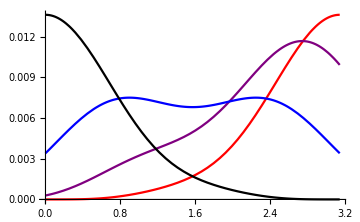
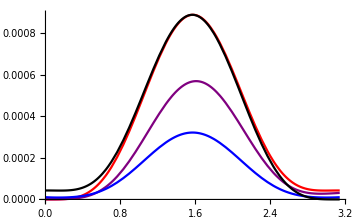

```mathematica
directions={{0,Pi/4,Pi/2,π},{Red,Purple,Blue,Black}};
{Plot[Chop[Ein/.{θ->π-θ}/.{ϕ0->0,θ->#1,ϕ->0,f_[a_.+b_.t]->0}],{θ0,0,π},PlotStyle->#2,ImageSize->Medium]&@@@Transpose[directions]//Show,Plot[Chop[Eout/.{ϕ0->0,θ->#1,ϕ->0,f_[a_.+b_.t]->0}],{θ0,0,π},PlotStyle->#2,ImageSize->Medium]&@@@Transpose[directions]//Show}
```

## Other tests

```mathematica
Y[s_,l_,m_,θ_,ϕ_]:=(-1)^m Simplify[√(((l+m)!(l-m)!(2l+1))/((l+s)!(l-s)!4π))(Sin[θ/2])^(2l)∑_(r=0)^(l-s) (Binomial[l-s,r]Binomial[l+s,r+s-m](-1)^(l-r-s)ⅇ^(ⅈ m ϕ)(Cot[θ/2])^(2r+s-m)),Assumptions->{ϕ∈Reals,θ∈Reals}];
```

```mathematica
SpinWeightedSphericalHarmonicsY[-1,1,-1,θ,ϕ]//TrigReduce
```

1/4 ⅇ^(-ⅈ ϕ) √(3/π) (-1+Cos[θ])

```mathematica
Flatten[Table[{l,m,Y[1,l,m,θ,ϕ],(-1)^(m-1)Y[1,l,m,θ,-ϕ]}//TrigReduce,{l,1,2},{m,-l,l}],1]//Grid
```

1 | -1 | -1/4 ⅇ^(-ⅈ ϕ) √(3/π) (1+Cos[θ]) | -1/4 ⅇ^(ⅈ ϕ) √(3/π) (1+Cos[θ])
1 | 0 | 1/2 √(3/(2 π)) Sin[θ] | -1/2 √(3/(2 π)) Sin[θ]
1 | 1 | 1/4 ⅇ^(ⅈ ϕ) √(3/π) (-1+Cos[θ]) | 1/4 ⅇ^(-ⅈ ϕ) √(3/π) (-1+Cos[θ])
2 | -2 | -1/8 ⅇ^(-2 ⅈ ϕ) √(5/π) (2 Sin[θ]+Sin[2 θ]) | 1/8 ⅇ^(2 ⅈ ϕ) √(5/π) (2 Sin[θ]+Sin[2 θ])
2 | -1 | -1/4 ⅇ^(-ⅈ ϕ) √(5/π) (Cos[θ]+Cos[2 θ]) | -1/4 ⅇ^(ⅈ ϕ) √(5/π) (Cos[θ]+Cos[2 θ])
2 | 0 | 1/4 √(15/(2 π)) Sin[2 θ] | -1/4 √(15/(2 π)) Sin[2 θ]
2 | 1 | -1/4 ⅇ^(ⅈ ϕ) √(5/π) (Cos[θ]-Cos[2 θ]) | -1/4 ⅇ^(-ⅈ ϕ) √(5/π) (Cos[θ]-Cos[2 θ])
2 | 2 | 1/8 ⅇ^(2 ⅈ ϕ) √(5/π) (2 Sin[θ]-Sin[2 θ]) | -1/8 ⅇ^(-2 ⅈ ϕ) √(5/π) (2 Sin[θ]-Sin[2 θ])

```mathematica
SpinD[s_,ℓ_]:=-Sin[θ]^s/Sqrt[ℓ(ℓ+1)-s(s+1)](D[(Sin[θ]^-s#), θ]+(I D[(Sin[θ]^-s#), ϕ])/Sin[θ])&
OverBar[SpinD][s_,ℓ_]:=-Sin[θ]^-s/(-Sqrt[ℓ(ℓ+1)-s(s+1)])(D[(Sin[θ]^s#), θ]-(I D[(Sin[θ]^s#), ϕ])/Sin[θ])&
```

```mathematica
Table[OverBar[SpinD][0,l]@SphericalHarmonicY[l,m,θ,ϕ]//Simplify//TrigReduce,{l,1,2},{m,-l,l}]==Table[Y[-1,l,m,θ,ϕ]//Simplify//TrigReduce,{l,1,2},{m,-l,l}]
```

True

0.0000431093 Cos[θ0/2]^8 Sin[θ/2]^4-0.0013993 Cos[θ0/2]^2 Cos[ϕ-ϕ0] Sin[θ/2]^2 Sin[θ] Sin[θ0/2]^4 Sin[θ0]+Cos[θ/2]^4 (0.0000431093 Sin[θ0/2]^8+0.000884826 Sin[θ0]^4)+Cos[θ0/2]^6 Sin[θ/2]^2 Sin[θ] Sin[θ0] (-0.0000491758 Cos[ϕ-ϕ0]+0.0000641639 Sin[ϕ-ϕ0])+Cos[θ/2]^2 Sin[θ] Sin[θ0/2]^6 Sin[θ0] (-0.0000491758 Cos[ϕ-ϕ0]+0.0000641639 Sin[ϕ-ϕ0])+Cos[θ0/2]^4 Sin[θ] Sin[θ0] (-0.0013993 Cos[θ/2]^2 Cos[ϕ-ϕ0] Sin[θ0/2]^2+Sin[θ] Sin[θ0] (0.0000378994-0.0000564443 Sin[2 (ϕ-ϕ0)]+0.0000398438 Csc[2 (ϕ-ϕ0)] Sin[4 (ϕ-ϕ0)]))+Sin[θ0]^2 (0.000884826 Sin[θ/2]^4 Sin[θ0]^2-0.000108439 Sin[θ/2]^2 Sin[θ] Sin[θ0/2]^2 Sin[θ0] Sin[ϕ-ϕ0]-6.77747×10^-6 Csc[θ/2]^2 Csc[θ0/2]^2 Sin[θ]^3 Sin[θ0]^3 Sin[ϕ-ϕ0]+Sin[θ]^2 Sin[θ0/2]^4 (0.0000378994-0.0000564443 Sin[2 (ϕ-ϕ0)]+0.0000398438 Csc[2 (ϕ-ϕ0)] Sin[4 (ϕ-ϕ0)]))